# ezARPACK unit tests

```mathematica
(* Make matrix A *)
MakeA[Nmat_]:=Table[Piecewise[{
{diagcoeffmean,i==j},
{offdiagcoeffmean+offdiagcoeffdiff,j-i==offdiagoffset},
{offdiagcoeffmean-offdiagcoeffdiff,i-j==offdiagoffset}
}],{i,1,Nmat},{j,1,Nmat}];

(* Make matrix M *)
MakeM[Nmat_]:=Table[If[i==j,1,If[Abs[i-j]==1,0.1,0]],{i,1,Nmat},{j,1,Nmat}];
```

## Symmetric matrices

```mathematica
(* Matrix size *)
Nmat=100;

(* Parameters of matrix A *)
diagcoeffmean=1.0;
offdiagoffset=3;
offdiagcoeffmean=-0.1;
offdiagcoeffdiff=0;

(* Matrix A *)
A=MakeA[Nmat];
Simplify[Det[A]≠0]

(* Matrix M *)
M=MakeM[Nmat];
Positive@Min@Eigenvalues[M]

(* Eigenvalues *)
Sort[Eigenvalues[A]]
Sort[Eigenvalues[{A,M}]]
Mean[Eigenvalues[{A,M}]]
```

True

True

{0.800805,0.800853,0.800853,0.803214,0.803405,0.803405,0.807207,0.807635,0.807635,0.812753,0.813506,0.813506,0.819806,0.820967,0.820967,0.82831,0.829957,0.829957,0.838197,0.840397,0.840397,0.849386,0.852198,0.852198,0.861787,0.865261,0.865261,0.875302,0.879473,0.879473,0.889821,0.894714,0.894714,0.905226,0.910852,0.910852,0.921395,0.927752,0.927752,0.938197,0.945267,0.945267,0.955496,0.96325,0.96325,0.973153,0.981546,0.981546,0.991027,1.,1.,1.00897,1.01845,1.01845,1.02685,1.03675,1.03675,1.0445,1.05473,1.05473,1.0618,1.07225,1.07225,1.07861,1.08915,1.08915,1.09477,1.10529,1.10529,1.11018,1.12053,1.12053,1.1247,1.13474,1.13474,1.13821,1.1478,1.1478,1.15061,1.1596,1.1596,1.1618,1.17004,1.17004,1.17169,1.17903,1.17903,1.18019,1.18649,1.18649,1.18725,1.19237,1.19237,1.19279,1.19659,1.19659,1.19679,1.19915,1.19915,1.19919}

{0.667424,0.669692,0.673453,0.67868,0.685337,0.693374,0.702736,0.713353,0.72515,0.738042,0.751935,0.766729,0.782315,0.798579,0.8154,0.832649,0.850186,0.867837,0.88213,0.882148,0.884189,0.884726,0.885713,0.88865,0.889084,0.894457,0.894797,0.900633,0.902382,0.903951,0.909862,0.911662,0.919041,0.91999,0.923733,0.93142,0.931745,0.939601,0.944124,0.944348,0.956103,0.957498,0.958175,0.971147,0.971374,0.974362,0.985241,0.985882,0.991579,1.,1.,1.00797,1.01365,1.01642,1.02238,1.02691,1.03417,1.03536,1.04085,1.04734,1.04819,1.05722,1.05927,1.06051,1.06754,1.06934,1.07601,1.07621,1.0833,1.08394,1.08442,1.0897,1.09038,1.09451,1.09451,1.09796,1.09805,1.10004,1.10005,1.10833,1.13317,1.15889,1.18511,1.21157,1.23804,1.26431,1.29014,1.31533,1.33966,1.36291,1.3849,1.40542,1.42431,1.44139,1.45652,1.46955,1.48038,1.48891,1.49505,1.49876}

1.02061

### Standard eigenproblem

```mathematica
(* Requested number of eigenvalues *)
nev=8;

eig=Eigenvalues[A];

(* Smallest *)
Sort[Sort[eig,#1<#2&][[1;;nev]]]
(* Largest *)
Sort[Sort[eig,#1>#2&][[1;;nev]]]
(* SmallestMagnitude *)
Sort[Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]]
(* LargestMagnitude *)
Sort[Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]]
(* BothEnds *)
Sort[Join[Sort[eig][[1;;nev/2]],Sort[eig][[-nev/2;;-1]]]]
```

{0.800805,0.800853,0.800853,0.803214,0.803405,0.803405,0.807207,0.807635}

{1.19237,1.19279,1.19659,1.19659,1.19679,1.19915,1.19915,1.19919}

{0.800805,0.800853,0.800853,0.803214,0.803405,0.803405,0.807207,0.807635}

{1.19237,1.19279,1.19659,1.19659,1.19679,1.19915,1.19915,1.19919}

{0.800805,0.800853,0.800853,0.803214,1.19679,1.19915,1.19915,1.19919}

### Generalized eigenproblem : invert mode

```mathematica
(* Requested number of eigenvalues *)
nev=8;

eig=Eigenvalues[{A,M}];

(* Smallest *)
Sort[Sort[eig,#1<#2&][[1;;nev]]]
(* Largest *)
Sort[Sort[eig,#1>#2&][[1;;nev]]]
(* SmallestMagnitude *)
Sort[Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]]
(* LargestMagnitude *)
Sort[Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]]
(* BothEnds *)
Sort[Join[Sort[eig][[1;;nev/2]],Sort[eig][[-nev/2;;-1]]]]
```

{0.667424,0.669692,0.673453,0.67868,0.685337,0.693374,0.702736,0.713353}

{1.42431,1.44139,1.45652,1.46955,1.48038,1.48891,1.49505,1.49876}

{0.667424,0.669692,0.673453,0.67868,0.685337,0.693374,0.702736,0.713353}

{1.42431,1.44139,1.45652,1.46955,1.48038,1.48891,1.49505,1.49876}

{0.667424,0.669692,0.673453,0.67868,1.48038,1.48891,1.49505,1.49876}

### Generalized eigenproblem: Shift-and-Invert mode

```mathematica
(* Requested number of eigenvalues *)
nev=8;
(* Spectral shift *)
σ=0.102;

eig=Eigenvalues[Inverse[A-σ M].M];
SpectralTransform[ν_]:=σ+1/ν;

(* Smallest *)
Sort[SpectralTransform[Sort[eig,#1<#2&][[;;nev]]]]
(* Largest *)
Sort[SpectralTransform[Sort[eig,#1>#2&][[;;nev]]]]
(* SmallestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]<Abs[#2]&][[;;nev]]]]
(* LargestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]>Abs[#2]&][[;;nev]]]]
(* BothEnds *)
BothEnds[l_]:=Join[l[[1;;nev/2]],l[[-nev/2;;-1]]];
Sort[SpectralTransform[BothEnds[Sort[eig]]]]
```

{1.42431,1.44139,1.45652,1.46955,1.48038,1.48891,1.49505,1.49876}

{0.667424,0.669692,0.673453,0.67868,0.685337,0.693374,0.702736,0.713353}

{1.42431,1.44139,1.45652,1.46955,1.48038,1.48891,1.49505,1.49876}

{0.667424,0.669692,0.673453,0.67868,0.685337,0.693374,0.702736,0.713353}

{0.667424,0.669692,0.673453,0.67868,1.48038,1.48891,1.49505,1.49876}

### Generalized eigenproblem: Buckling mode

```mathematica
(* Requested number of eigenvalues *)
nev=10;
(* Spectral shift *)
σ=0.102;

K=M;
KG=A;

eig=Eigenvalues[Inverse[K-σ KG].K];
SpectralTransform[ν_]:=σ/(1-1/ν);

(* Smallest *)
Sort[SpectralTransform[Sort[eig,#1<#2&][[;;nev]]]]
(* Largest *)
Sort[SpectralTransform[Sort[eig,#1>#2&][[;;nev]]]]
(* SmallestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]<Abs[#2]&][[;;nev]]]]
(* LargestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]>Abs[#2]&][[;;nev]]]]
(* BothEnds *)
BothEnds[l_]:=Join[l[[1;;nev/2]],l[[-nev/2;;-1]]];
Sort[SpectralTransform[BothEnds[Sort[eig]]]]
```

{1.35494,1.37902,1.40183,1.42301,1.44222,1.45914,1.47345,1.48489,1.49322,1.4983}

{0.667218,0.668873,0.671634,0.675501,0.680479,0.686569,0.693773,0.702094,0.711529,0.722075}

{1.35494,1.37902,1.40183,1.42301,1.44222,1.45914,1.47345,1.48489,1.49322,1.4983}

{0.667218,0.668873,0.671634,0.675501,0.680479,0.686569,0.693773,0.702094,0.711529,0.722075}

{0.667218,0.668873,0.671634,0.675501,0.680479,1.45914,1.47345,1.48489,1.49322,1.4983}

### Generalized eigenproblem: Cayley transformed mode

```mathematica
(* Requested number of eigenvalues *)
nev=10;
(* Spectral shift *)
σ=0.102;

eig=Eigenvalues[Inverse[A-σ M].(A+σ M)];
SpectralTransform[ν_]:=σ(ν+1)/(ν-1);

(* Smallest *)
Sort[SpectralTransform[Sort[eig,#1<#2&][[;;nev]]]]
(* Largest *)
Sort[SpectralTransform[Sort[eig,#1>#2&][[;;nev]]]]
(* SmallestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]<Abs[#2]&][[;;nev]]]]
(* LargestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]>Abs[#2]&][[;;nev]]]]
(* BothEnds *)
BothEnds[l_]:=Join[l[[1;;nev/2]],l[[-nev/2;;-1]]];
Sort[SpectralTransform[BothEnds[Sort[eig]]]]
```

{1.3849,1.40542,1.42431,1.44139,1.45652,1.46955,1.48038,1.48891,1.49505,1.49876}

{0.667424,0.669692,0.673453,0.67868,0.685337,0.693374,0.702736,0.713353,0.72515,0.738042}

{1.3849,1.40542,1.42431,1.44139,1.45652,1.46955,1.48038,1.48891,1.49505,1.49876}

{0.667424,0.669692,0.673453,0.67868,0.685337,0.693374,0.702736,0.713353,0.72515,0.738042}

{0.667424,0.669692,0.673453,0.67868,0.685337,1.46955,1.48038,1.48891,1.49505,1.49876}

## Asymmetric matrices

```mathematica
(* Matrix size *)
Nmat=100;

(* Parameters of matrix A *)
diagcoeffmean=1.0;
offdiagoffset=3;
offdiagcoeffmean=-1.0;
offdiagcoeffdiff=0.1;

(* Matrix A *)
A=MakeA[Nmat];
Simplify[Det[A]≠0]

(* Matrix M *)
M=MakeM[Nmat];
Positive@Min@Eigenvalues[M]

(* Eigenvalues *)
Sort[Eigenvalues[A]]
Sort[Eigenvalues[{A,M}]]
Mean[Eigenvalues[{A,M}]]
```

True

True

{-0.981964,-0.981486,-0.981486,-0.957995,-0.956092,-0.956092,-0.918262,-0.914009,-0.914009,-0.863084,-0.855596,-0.855596,-0.792905,-0.781352,-0.781352,-0.708292,-0.691911,-0.691911,-0.609923,-0.588034,-0.588034,-0.498593,-0.470609,-0.470609,-0.375197,-0.340637,-0.340637,-0.240729,-0.199228,-0.199228,-0.0962712,-0.0475868,-0.0475868,0.0570133,0.112992,0.112992,0.21789,0.281138,0.281138,0.385064,0.455418,0.455418,0.557189,0.634343,0.634343,0.732879,0.816388,0.816388,0.91072,1.,1.,1.08928,1.18361,1.18361,1.26712,1.36566,1.36566,1.44281,1.54458,1.54458,1.61494,1.71886,1.71886,1.78211,1.88701,1.88701,1.94299,2.04759,2.04759,2.09627,2.19923,2.19923,2.24073,2.34064,2.34064,2.3752,2.47061,2.47061,2.49859,2.58803,2.58803,2.60992,2.69191,2.69191,2.70829,2.78135,2.78135,2.79291,2.8556,2.8556,2.86308,2.91401,2.91401,2.91826,2.95609,2.95609,2.958,2.98149,2.98149,2.98196}

{-1.09177+0.00699222 ⅈ,-1.09177-0.00699222 ⅈ,-1.06383+0.00678953 ⅈ,-1.06383-0.00678953 ⅈ,-1.01755-0.00645554 ⅈ,-1.01755+0.00645554 ⅈ,-0.953389-0.00599861 ⅈ,-0.953389+0.00599861 ⅈ,-0.871992+0.00539581 ⅈ,-0.871992-0.00539581 ⅈ,-0.818006+0. ⅈ,-0.797798+0. ⅈ,-0.774056+0.00444102 ⅈ,-0.774056-0.00444102 ⅈ,-0.763373+0. ⅈ,-0.715508+0. ⅈ,-0.667451+0. ⅈ,-0.65764+0. ⅈ,-0.65104+0. ⅈ,-0.584916+0. ⅈ,-0.534232+0. ⅈ,-0.52804+0. ⅈ,-0.498699+0. ⅈ,-0.40287+0. ⅈ,-0.398814+0. ⅈ,-0.380423+0. ⅈ,-0.294317+0. ⅈ,-0.251892+0. ⅈ,-0.222434+0. ⅈ,-0.174796+0. ⅈ,-0.0983111+0. ⅈ,-0.0529617+0. ⅈ,-0.0428213+0. ⅈ,0.0562959+0. ⅈ,0.105478+0. ⅈ,0.124819+0. ⅈ,0.209565+0. ⅈ,0.271439+0. ⅈ,0.305486+0. ⅈ,0.367976+0. ⅈ,0.449927+0. ⅈ,0.47996+0. ⅈ,0.539505+0. ⅈ,0.638237+0. ⅈ,0.645105+0. ⅈ,0.722852+0. ⅈ,0.808457+0. ⅈ,0.833824+0. ⅈ,0.908324+0. ⅈ,0.96981+0. ⅈ,1.03905+0. ⅈ,1.09055+0. ⅈ,1.13039+0. ⅈ,1.25127+0. ⅈ,1.26723+0. ⅈ,1.28938+0. ⅈ,1.44216+0.00585305 ⅈ,1.44216-0.00585305 ⅈ,1.46611+0. ⅈ,1.6018+0.00592195 ⅈ,1.6018-0.00592195 ⅈ,1.67688+0. ⅈ,1.74876+0. ⅈ,1.765+0. ⅈ,1.87055+0. ⅈ,1.88539+0. ⅈ,1.93993+0. ⅈ,2.02155-0.00945247 ⅈ,2.02155+0.00945247 ⅈ,2.13548+0. ⅈ,2.1507-0.0105362 ⅈ,2.1507+0.0105362 ⅈ,2.26681-0.00965115 ⅈ,2.26681+0.00965115 ⅈ,2.33476+0. ⅈ,2.3739+0.00585668 ⅈ,2.3739-0.00585668 ⅈ,2.45972-0.0125313 ⅈ,2.45972+0.0125313 ⅈ,2.54043+0.0124884 ⅈ,2.54043-0.0124884 ⅈ,2.54402+0. ⅈ,2.60615+0.0133239 ⅈ,2.60615-0.0133239 ⅈ,2.65653-0.0141045 ⅈ,2.65653+0.0141045 ⅈ,2.69389+0.0143611 ⅈ,2.69389-0.0143611 ⅈ,2.7161-0.0144967 ⅈ,2.7161+0.0144967 ⅈ,2.73452+0. ⅈ,2.91058+0. ⅈ,3.07443+0. ⅈ,3.22335+0. ⅈ,3.35568+0. ⅈ,3.47001+0. ⅈ,3.56517+0. ⅈ,3.6402+0. ⅈ,3.69433+0. ⅈ,3.72703+0. ⅈ}

1.02245-8.67362×10^-21 ⅈ

### Standard eigenproblem

```mathematica
(* Requested number of eigenvalues *)
nev=8;

eig=Eigenvalues[A];

(* LargestMagnitude *)
Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]
(* SmallestMagnitude *)
Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]
(* LargestReal *)
Sort[eig,Abs[Re[#1]]>Abs[Re[#2]]&][[1;;nev]]
(* SmallestReal *)
Sort[eig,Abs[Re[#1]]<Abs[Re[#2]]&][[1;;nev]]
(* LargestImag *)
Sort[eig,Abs[Im[#1]]>Abs[Im[#2]]&][[1;;nev]]
(* SmallestImag *)
Sort[eig,Abs[Im[#1]]<Abs[Im[#2]]&][[1;;nev]]
```

{2.98196,2.98149,2.98149,2.958,2.95609,2.95609,2.91826,2.91401}

{-0.0475868,-0.0475868,0.0570133,-0.0962712,0.112992,0.112992,-0.199228,-0.199228}

{2.98196,2.98149,2.98149,2.958,2.95609,2.95609,2.91826,2.91401}

{-0.0475868,-0.0475868,0.0570133,-0.0962712,0.112992,0.112992,-0.199228,-0.199228}

{-0.0475868,-0.0475868,0.0570133,-0.0962712,0.112992,0.112992,-0.199228,-0.199228}

{-0.0475868,-0.0475868,0.0570133,-0.0962712,0.112992,0.112992,-0.199228,-0.199228}

### Generalized eigenproblem : invert mode

```mathematica
(* Requested number of eigenvalues *)
nev=8;

eig=Eigenvalues[Inverse[M].A];

(* LargestMagnitude *)
Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]
(* SmallestMagnitude *)
Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]
(* LargestReal *)
Sort[eig,Abs[Re[#1]]>Abs[Re[#2]]&][[1;;nev]]
(* SmallestReal *)
Sort[eig,Abs[Re[#1]]<Abs[Re[#2]]&][[1;;nev]]
(* LargestImag *)
Sort[eig,Abs[Im[#1]]>Abs[Im[#2]]&][[1;;nev]]
(* SmallestImag *)
Sort[eig,Abs[Im[#1]]<Abs[Im[#2]]&][[1;;nev]]
```

{3.72703+0. ⅈ,3.69433+0. ⅈ,3.6402+0. ⅈ,3.56517+0. ⅈ,3.47001+0. ⅈ,3.35568+0. ⅈ,3.22335+0. ⅈ,3.07443+0. ⅈ}

{-0.0428213+0. ⅈ,-0.0529617+0. ⅈ,0.0562959+0. ⅈ,-0.0983111+0. ⅈ,0.105478+0. ⅈ,0.124819+0. ⅈ,-0.174796+0. ⅈ,0.209565+0. ⅈ}

{3.72703+0. ⅈ,3.69433+0. ⅈ,3.6402+0. ⅈ,3.56517+0. ⅈ,3.47001+0. ⅈ,3.35568+0. ⅈ,3.22335+0. ⅈ,3.07443+0. ⅈ}

{-0.0428213+0. ⅈ,-0.0529617+0. ⅈ,0.0562959+0. ⅈ,-0.0983111+0. ⅈ,0.105478+0. ⅈ,0.124819+0. ⅈ,-0.174796+0. ⅈ,0.209565+0. ⅈ}

{2.7161-0.0144967 ⅈ,2.7161+0.0144967 ⅈ,2.69389-0.0143611 ⅈ,2.69389+0.0143611 ⅈ,2.65653-0.0141045 ⅈ,2.65653+0.0141045 ⅈ,2.60615-0.0133239 ⅈ,2.60615+0.0133239 ⅈ}

{-0.0428213+0. ⅈ,-0.0529617+0. ⅈ,0.0562959+0. ⅈ,-0.0983111+0. ⅈ,0.105478+0. ⅈ,0.124819+0. ⅈ,-0.174796+0. ⅈ,0.209565+0. ⅈ}

### Generalized eigenproblem : Shift-and-Invert mode

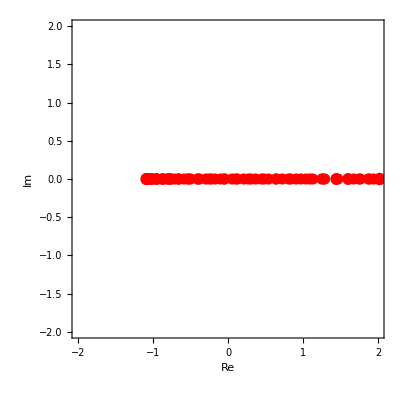

{3.72703+0. ⅈ,3.69433+0. ⅈ,3.6402+0. ⅈ,3.56517+0. ⅈ,3.47001+0. ⅈ,3.35568+0. ⅈ,3.22335+0. ⅈ,3.07443+0. ⅈ}

{3.72703+0. ⅈ,3.69433+0. ⅈ,3.6402+0. ⅈ,3.56517+0. ⅈ,3.47001+0. ⅈ,3.35568+0. ⅈ,3.22335+0. ⅈ,3.07443+0. ⅈ}

{2.7161+0.0144967 ⅈ,2.69389+0.0143611 ⅈ,2.65653+0.0141045 ⅈ,2.60615+0.0133239 ⅈ,2.45972+0.0125313 ⅈ,2.54043+0.0124884 ⅈ,2.1507+0.0105362 ⅈ,2.26681+0.00965115 ⅈ}

```mathematica
(* Requested number of eigenvalues *)
nev=8;
(* Spectral shift *)
σ=0.5+ⅈ 0.5;

eig=Eigenvalues[{A,M}];

ListPlot[{Re[#],Im[#]}&/@eig,AxesOrigin->{0,0},PlotRange->{{-2,2},{-2,2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]]

Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]
Sort[eig,Re[#1]>Re[#2]&][[1;;nev]]
Sort[eig,Im[#1]>Im[#2]&][[1;;nev]]
```

## Complex matrices

```mathematica
(* Matrix size *)
Nmat=100;

(* Parameters of matrix A *)
diagcoeffmean=2.0;
offdiagoffset=3;
offdiagcoeffmean=0;
offdiagcoeffdiff=-0.01+0.1ⅈ;

(* Matrix A *)
A=MakeA[Nmat];
Simplify[Det[A]≠0]

(* Matrix M *)
M=MakeM[Nmat];
Positive@Min@Eigenvalues[M]
Det[M]

(* Eigenvalues *)
Sort[Eigenvalues[A]]
Sort[Eigenvalues[{A,M}]]
Mean[Eigenvalues[{A,M}]]
```

True

True

0.366014

{1.80081-0.0199195 ⅈ,1.80085-0.0199147 ⅈ,1.80085-0.0199147 ⅈ,1.80321-0.0196786 ⅈ,1.80341-0.0196595 ⅈ,1.80341-0.0196595 ⅈ,1.80721-0.0192793 ⅈ,1.80763-0.0192365 ⅈ,1.80763-0.0192365 ⅈ,1.81275-0.0187247 ⅈ,1.81351-0.0186494 ⅈ,1.81351-0.0186494 ⅈ,1.81981-0.0180194 ⅈ,1.82097-0.0179033 ⅈ,1.82097-0.0179033 ⅈ,1.82831-0.017169 ⅈ,1.82996-0.0170043 ⅈ,1.82996-0.0170043 ⅈ,1.8382-0.0161803 ⅈ,1.8404-0.0159603 ⅈ,1.8404-0.0159603 ⅈ,1.84939-0.0150614 ⅈ,1.8522-0.0147802 ⅈ,1.8522-0.0147802 ⅈ,1.86179-0.0138213 ⅈ,1.86526-0.0134739 ⅈ,1.86526-0.0134739 ⅈ,1.8753-0.0124698 ⅈ,1.87947-0.0120527 ⅈ,1.87947-0.0120527 ⅈ,1.88982-0.0110179 ⅈ,1.89471-0.0105286 ⅈ,1.89471-0.0105286 ⅈ,1.90523-0.00947737 ⅈ,1.91085-0.00891477 ⅈ,1.91085-0.00891477 ⅈ,1.92139-0.0078605 ⅈ,1.92775-0.00722483 ⅈ,1.92775-0.00722483 ⅈ,1.9382-0.00618034 ⅈ,1.94527-0.00547326 ⅈ,1.94527-0.00547326 ⅈ,1.9555-0.00445042 ⅈ,1.96325-0.00367499 ⅈ,1.96325-0.00367499 ⅈ,1.97315-0.00268467 ⅈ,1.98155-0.00184537 ⅈ,1.98155-0.00184537 ⅈ,1.99103-0.000897297 ⅈ,2.+4.85658×10^-16 ⅈ,2.-6.29997×10^-16 ⅈ,2.00897+0.000897297 ⅈ,2.01845+0.00184537 ⅈ,2.01845+0.00184537 ⅈ,2.02685+0.00268467 ⅈ,2.03675+0.00367499 ⅈ,2.03675+0.00367499 ⅈ,2.0445+0.00445042 ⅈ,2.05473+0.00547326 ⅈ,2.05473+0.00547326 ⅈ,2.0618+0.00618034 ⅈ,2.07225+0.00722483 ⅈ,2.07225+0.00722483 ⅈ,2.07861+0.0078605 ⅈ,2.08915+0.00891477 ⅈ,2.08915+0.00891477 ⅈ,2.09477+0.00947737 ⅈ,2.10529+0.0105286 ⅈ,2.10529+0.0105286 ⅈ,2.11018+0.0110179 ⅈ,2.12053+0.0120527 ⅈ,2.12053+0.0120527 ⅈ,2.1247+0.0124698 ⅈ,2.13474+0.0134739 ⅈ,2.13474+0.0134739 ⅈ,2.13821+0.0138213 ⅈ,2.1478+0.0147802 ⅈ,2.1478+0.0147802 ⅈ,2.15061+0.0150614 ⅈ,2.1596+0.0159603 ⅈ,2.1596+0.0159603 ⅈ,2.1618+0.0161803 ⅈ,2.17004+0.0170043 ⅈ,2.17004+0.0170043 ⅈ,2.17169+0.017169 ⅈ,2.17903+0.0179033 ⅈ,2.17903+0.0179033 ⅈ,2.18019+0.0180194 ⅈ,2.18649+0.0186494 ⅈ,2.18649+0.0186494 ⅈ,2.18725+0.0187247 ⅈ,2.19237+0.0192365 ⅈ,2.19237+0.0192365 ⅈ,2.19279+0.0192793 ⅈ,2.19659+0.0196595 ⅈ,2.19659+0.0196595 ⅈ,2.19679+0.0196786 ⅈ,2.19915+0.0199147 ⅈ,2.19915+0.0199147 ⅈ,2.19919+0.0199195 ⅈ}

{1.53028-0.0164583 ⅈ,1.53271-0.016243 ⅈ,1.53674-0.015886 ⅈ,1.54234-0.0153902 ⅈ,1.54948-0.0147592 ⅈ,1.55808-0.013998 ⅈ,1.5681-0.0131124 ⅈ,1.57946-0.0121095 ⅈ,1.59207-0.0109968 ⅈ,1.60583-0.00978325 ⅈ,1.62064-0.00847831 ⅈ,1.63638-0.0070924 ⅈ,1.65293-0.00563678 ⅈ,1.67016-0.00412357 ⅈ,1.68791-0.00256604 ⅈ,1.70603-0.000979181 ⅈ,1.72437+0.000618516 ⅈ,1.74274+0.00219906 ⅈ,1.76097+0.00370918 ⅈ,1.76594-0.0156659 ⅈ,1.76796-0.0152608 ⅈ,1.77145-0.0149859 ⅈ,1.77618-0.0136793 ⅈ,1.77894+0.00511333 ⅈ,1.78176-0.0136416 ⅈ,1.79021-0.0113315 ⅈ,1.79551-0.0108891 ⅈ,1.79648+0.00650028 ⅈ,1.80813-0.0108034 ⅈ,1.81318-0.00410511 ⅈ,1.81347+0.0077721 ⅈ,1.82649-0.00979923 ⅈ,1.82892+0.00888362 ⅈ,1.83513+0.00349066 ⅈ,1.84393+0.0108842 ⅈ,1.84602-0.00868501 ⅈ,1.85388+0.00948106 ⅈ,1.85858+0.0118585 ⅈ,1.86691+0.0131927 ⅈ,1.86707-0.00782139 ⅈ,1.8718+0.0133258 ⅈ,1.87682+0.0148069 ⅈ,1.88058+0.0150236 ⅈ,1.88323+0.015663 ⅈ,1.88491+0.0158643 ⅈ,1.88928-0.00693766 ⅈ,1.91243-0.00572613 ⅈ,1.93658-0.00422438 ⅈ,1.96154-0.00258331 ⅈ,1.98709-0.000870731 ⅈ,2.01297+0.000875148 ⅈ,2.03894+0.00262423 ⅈ,2.06477+0.00434678 ⅈ,2.09019+0.00600783 ⅈ,2.11493+0.00755774 ⅈ,2.13874+0.00891315 ⅈ,2.15815-0.0210242 ⅈ,2.16039-0.0207246 ⅈ,2.16143+0.00997567 ⅈ,2.16348-0.019685 ⅈ,2.16879-0.0195874 ⅈ,2.17401-0.016579 ⅈ,2.18146-0.0180357 ⅈ,2.18284+0.0108215 ⅈ,2.1896-0.0112093 ⅈ,2.19697-0.0162552 ⅈ,2.20258+0.0115691 ⅈ,2.20828-0.00370975 ⅈ,2.21496-0.0148539 ⅈ,2.22008+0.0122423 ⅈ,2.22668+0.00390789 ⅈ,2.23491+0.0130665 ⅈ,2.23541-0.0134666 ⅈ,2.24195+0.00968049 ⅈ,2.24684+0.0138281 ⅈ,2.25212+0.0130711 ⅈ,2.25488+0.0143638 ⅈ,2.25712+0.0144663 ⅈ,2.25766-0.0119341 ⅈ,2.2813-0.0101812 ⅈ,2.30615-0.008203 ⅈ,2.33197-0.00609625 ⅈ,2.35845-0.00391676 ⅈ,2.3853-0.00169775 ⅈ,2.41227+0.000535335 ⅈ,2.43908+0.00276009 ⅈ,2.46549+0.00495555 ⅈ,2.49125+0.0071016 ⅈ,2.51615+0.0091788 ⅈ,2.53995+0.0111684 ⅈ,2.56245+0.0130524 ⅈ,2.58344+0.0148136 ⅈ,2.60275+0.0164361 ⅈ,2.62021+0.017905 ⅈ,2.63566+0.0192068 ⅈ,2.64897+0.0203295 ⅈ,2.66002+0.0212627 ⅈ,2.66872+0.0219976 ⅈ,2.67499+0.0225276 ⅈ,2.67877+0.0228475 ⅈ}

2.04082+1.47105×10^-17 ⅈ

### Standard eigenproblem

```mathematica
(* Requested number of eigenvalues *)
nev=8;

eig=Eigenvalues[A];

(* LargestMagnitude *)
Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]
(* SmallestMagnitude *)
Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]
(* LargestReal *)
Sort[eig,Re[#1]>Re[#2]&][[1;;nev]]
(* SmallestReal *)
Sort[eig,Re[#1]<Re[#2]&][[1;;nev]]
(* LargestImag *)
Sort[eig,Im[#1]>Im[#2]&][[1;;nev]]
(* SmallestImag *)
Sort[eig,Im[#1]<Im[#2]&][[1;;nev]]
```

{2.19919+0.0199195 ⅈ,2.19915+0.0199147 ⅈ,2.19915+0.0199147 ⅈ,2.19679+0.0196786 ⅈ,2.19659+0.0196595 ⅈ,2.19659+0.0196595 ⅈ,2.19279+0.0192793 ⅈ,2.19237+0.0192365 ⅈ}

{1.80081-0.0199195 ⅈ,1.80085-0.0199147 ⅈ,1.80085-0.0199147 ⅈ,1.80321-0.0196786 ⅈ,1.80341-0.0196595 ⅈ,1.80341-0.0196595 ⅈ,1.80721-0.0192793 ⅈ,1.80763-0.0192365 ⅈ}

{2.19919+0.0199195 ⅈ,2.19915+0.0199147 ⅈ,2.19915+0.0199147 ⅈ,2.19679+0.0196786 ⅈ,2.19659+0.0196595 ⅈ,2.19659+0.0196595 ⅈ,2.19279+0.0192793 ⅈ,2.19237+0.0192365 ⅈ}

{1.80081-0.0199195 ⅈ,1.80085-0.0199147 ⅈ,1.80085-0.0199147 ⅈ,1.80321-0.0196786 ⅈ,1.80341-0.0196595 ⅈ,1.80341-0.0196595 ⅈ,1.80721-0.0192793 ⅈ,1.80763-0.0192365 ⅈ}

{2.19919+0.0199195 ⅈ,2.19915+0.0199147 ⅈ,2.19915+0.0199147 ⅈ,2.19679+0.0196786 ⅈ,2.19659+0.0196595 ⅈ,2.19659+0.0196595 ⅈ,2.19279+0.0192793 ⅈ,2.19237+0.0192365 ⅈ}

{1.80081-0.0199195 ⅈ,1.80085-0.0199147 ⅈ,1.80085-0.0199147 ⅈ,1.80321-0.0196786 ⅈ,1.80341-0.0196595 ⅈ,1.80341-0.0196595 ⅈ,1.80721-0.0192793 ⅈ,1.80763-0.0192365 ⅈ}

### Generalized eigenproblem : invert mode

```mathematica
(* Requested number of eigenvalues *)
nev=8;

eig=Eigenvalues[Inverse[M].A];

(* LargestMagnitude *)
Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]
(* SmallestMagnitude *)
Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]
(* LargestReal *)
Sort[eig,Re[#1]>Re[#2]&][[1;;nev]]
(* SmallestReal *)
Sort[eig,Re[#1]<Re[#2]&][[1;;nev]]
(* LargestImag *)
Sort[eig,Im[#1]>Im[#2]&][[1;;nev]]
(* SmallestImag *)
Sort[eig,Im[#1]<Im[#2]&][[1;;nev]]
```

{2.67877+0.0228475 ⅈ,2.67499+0.0225276 ⅈ,2.66872+0.0219976 ⅈ,2.66002+0.0212627 ⅈ,2.64897+0.0203295 ⅈ,2.63566+0.0192068 ⅈ,2.62021+0.017905 ⅈ,2.60275+0.0164361 ⅈ}

{1.53028-0.0164583 ⅈ,1.53271-0.016243 ⅈ,1.53674-0.015886 ⅈ,1.54234-0.0153902 ⅈ,1.54948-0.0147592 ⅈ,1.55808-0.013998 ⅈ,1.5681-0.0131124 ⅈ,1.57946-0.0121095 ⅈ}

{2.67877+0.0228475 ⅈ,2.67499+0.0225276 ⅈ,2.66872+0.0219976 ⅈ,2.66002+0.0212627 ⅈ,2.64897+0.0203295 ⅈ,2.63566+0.0192068 ⅈ,2.62021+0.017905 ⅈ,2.60275+0.0164361 ⅈ}

{1.53028-0.0164583 ⅈ,1.53271-0.016243 ⅈ,1.53674-0.015886 ⅈ,1.54234-0.0153902 ⅈ,1.54948-0.0147592 ⅈ,1.55808-0.013998 ⅈ,1.5681-0.0131124 ⅈ,1.57946-0.0121095 ⅈ}

{2.67877+0.0228475 ⅈ,2.67499+0.0225276 ⅈ,2.66872+0.0219976 ⅈ,2.66002+0.0212627 ⅈ,2.64897+0.0203295 ⅈ,2.63566+0.0192068 ⅈ,2.62021+0.017905 ⅈ,2.60275+0.0164361 ⅈ}

{2.15815-0.0210242 ⅈ,2.16039-0.0207246 ⅈ,2.16348-0.019685 ⅈ,2.16879-0.0195874 ⅈ,2.18146-0.0180357 ⅈ,2.17401-0.016579 ⅈ,1.53028-0.0164583 ⅈ,2.19697-0.0162552 ⅈ}

### Generalized eigenproblem: Shift-and-Invert mode

```mathematica
(* Requested number of eigenvalues *)
nev=8;
(* Spectral shift *)
σ=0.1+0.1ⅈ;

eig=Eigenvalues[Inverse[A-σ M].M];
SpectralTransform[ν_]:=σ+1/ν;

(* LargestMagnitude *)
SpectralTransform[Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]]
(* SmallestMagnitude *)
SpectralTransform[Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]]
(* LargestReal *)
SpectralTransform[Sort[eig,Re[#1]>Re[#2]&][[1;;nev]]]
(* SmallestReal *)
SpectralTransform[Sort[eig,Re[#1]<Re[#2]&][[1;;nev]]]
(* LargestImag *)
SpectralTransform[Sort[eig,Im[#1]>Im[#2]&][[1;;nev]]]
(* SmallestImag *)
SpectralTransform[Sort[eig,Im[#1]<Im[#2]&][[1;;nev]]]
```

{1.53028-0.0164583 ⅈ,1.53271-0.016243 ⅈ,1.53674-0.015886 ⅈ,1.54234-0.0153902 ⅈ,1.54948-0.0147592 ⅈ,1.55808-0.013998 ⅈ,1.5681-0.0131124 ⅈ,1.57946-0.0121095 ⅈ}

{2.67877+0.0228475 ⅈ,2.67499+0.0225276 ⅈ,2.66872+0.0219976 ⅈ,2.66002+0.0212627 ⅈ,2.64897+0.0203295 ⅈ,2.63566+0.0192068 ⅈ,2.62021+0.017905 ⅈ,2.60275+0.0164361 ⅈ}

{1.53028-0.0164583 ⅈ,1.53271-0.016243 ⅈ,1.53674-0.015886 ⅈ,1.54234-0.0153902 ⅈ,1.54948-0.0147592 ⅈ,1.55808-0.013998 ⅈ,1.5681-0.0131124 ⅈ,1.57946-0.0121095 ⅈ}

{2.67877+0.0228475 ⅈ,2.67499+0.0225276 ⅈ,2.66872+0.0219976 ⅈ,2.66002+0.0212627 ⅈ,2.64897+0.0203295 ⅈ,2.63566+0.0192068 ⅈ,2.62021+0.017905 ⅈ,2.60275+0.0164361 ⅈ}

{1.53028-0.0164583 ⅈ,1.53271-0.016243 ⅈ,1.53674-0.015886 ⅈ,1.54234-0.0153902 ⅈ,1.54948-0.0147592 ⅈ,1.55808-0.013998 ⅈ,1.5681-0.0131124 ⅈ,1.57946-0.0121095 ⅈ}

{2.67877+0.0228475 ⅈ,2.67499+0.0225276 ⅈ,2.66872+0.0219976 ⅈ,2.66002+0.0212627 ⅈ,2.64897+0.0203295 ⅈ,2.63566+0.0192068 ⅈ,2.62021+0.017905 ⅈ,2.60275+0.0164361 ⅈ}